### Euler折线法求解

```mathematica
ode={x'[t]==x[t],x[0]==1}
```

{x'[t]==x[t],x[0]==1}

### 精确解

```mathematica
DSolve[ode,x[t],t]
```

{{x[t]→ⅇ^t}}

### 区间等分，构造分点

```mathematica
tspan={-1,1};
nequalpart=8;
ts[s_]:=Part[Table[i,{i,tspan[[1]],tspan[[2]],(tspan[[2]]-tspan[[1]])/nequalpart}],s+nequalpart/2+1]
```

### 函数定义:

```mathematica
"D[x[t],t]==f[x[t],t]"
```

```mathematica
f[t_,x_]:=x;x0=1;
x[t_]:=Piecewise[{{x[t-1]+f[t-1,x[t-1]]*(ts[t]-ts[t-1]),t>0},{x[t+1]+f[t+1,x[t+1]]*(-ts[t+1]+ts[t]),t<0},{x0,t==0}}];
```

### Euler折线方程

```mathematica
φn[s_,dirc_]:=Piecewise[{{x[0]+Sum[f[ts[k],x[k]]*(ts[k+1]-ts[k]),{k,0,s-1}]+f[ts[s],x[s]]*(t-ts[s]),dirc=="r"},{x[0]+Sum[f[ts[k],x[k]]*(ts[k-1]-ts[k]),{k,1-s,0}]+f[ts[-s],x[-s]]*(t-ts[-s]),dirc=="l"}}]
```

### 结果及绘图展示

```mathematica
tlist=Flatten@{Table[ts[i]<=t<ts[i+1],{i,-nequalpart/2,nequalpart/2-2}],ts[nequalpart/2-1]<=t<=ts[nequalpart/2]}
φnlist=Flatten[{Table[Expand@φn[s,"l"],{s,nequalpart/2-1,0,-1}],Table[Expand@φn[s,"r"],{s,0,nequalpart/2-1,1}]}]
```

{-1≤t<-3/4,-3/4≤t<-1/2,-1/2≤t<-1/4,-1/4≤t<0,0≤t<1/4,1/4≤t<1/2,1/2≤t<3/4,3/4≤t≤1}

{189/256+(27 t)/64,27/32+(9 t)/16,15/16+(3 t)/4,1+t,1+t,15/16+(5 t)/4,25/32+(25 t)/16,125/256+(125 t)/64}

```mathematica
TraditionalForm[φ[t_]=Piecewise[Table[{φnlist[[i]],tlist[[i]]},{i,1,nequalpart}]]]
```

Piecewise[{{(27 t)/64+189/256, -1≤t<-3/4}, {(9 t)/16+27/32, -3/4≤t<-1/2}, {(3 t)/4+15/16, -1/2≤t<-1/4}, {t+1, -1/4≤t<0∨0≤t<1/4}, {(5 t)/4+15/16, 1/4≤t<1/2}, {(25 t)/16+25/32, 1/2≤t<3/4}, {(125 t)/64+125/256, 3/4≤t≤1}}]

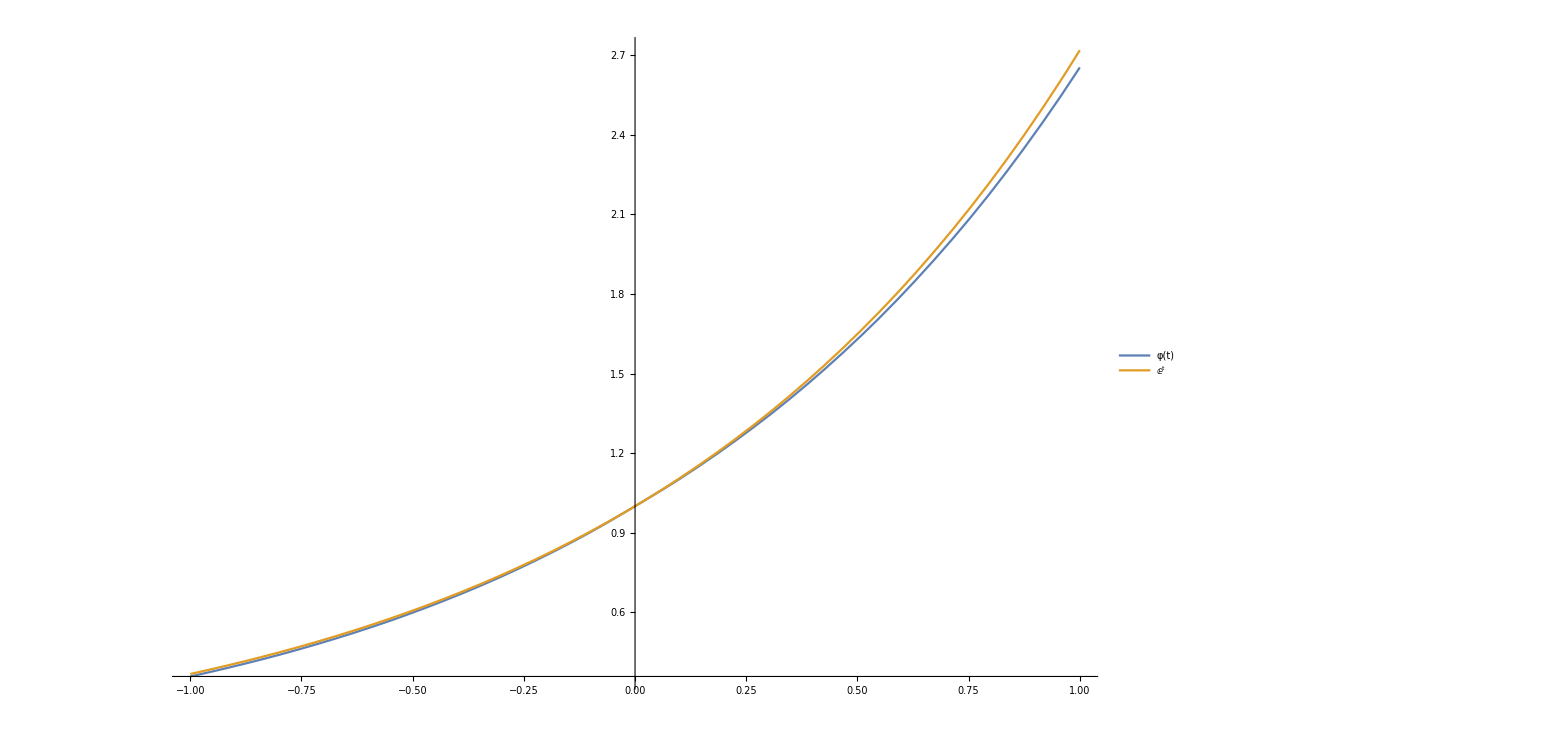

```mathematica
Plot[{φ[t],ⅇ^t},{t,-1,1},PlotLegends->"Expressions"]
```